# Mutation-selection-drift balance with irreversible (and non-reccurent) (deleterious) mutations

With sufficiently rare mutation (U<<1), Wright 1938 (PNAS 24:253) equation 29 with C=4U and t=0 gives the distribution of mutant allele frequency, q, as

```mathematica
f[q_]:=U Exp[4 γ q] 4/(q(1-q))
```

where U is the population scaled mutation rate (U = N u, where u is the probability of mutation per individual) and γ is the population scaled selection coefficient (γ = Ne s, where Ne is the effective population size and s is the selection coefficient of the mutant, s>0 if beneficial, s<0 if deleterious).

Thinking about a haploid population we divide N by two to get

```mathematica
f[q_]:=U Exp[2 γ q] 2/(q(1-q))
```

This looks like

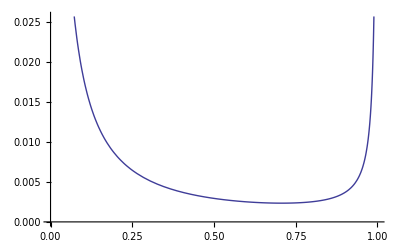

```mathematica
Plot[f[q]/.γ->s Ne/.U->u Ne/.s->-0.001/.Ne->1000/.u->10^-6,{q,0,1},PlotRange->{0,Automatic}]
```

With weak sufficiently weak selection (|γ|<<1?) equation 39 in Wright 1938 gives (after converting to a haploid population by dividing N by 2)

```mathematica
f[q_]:=(1-Exp[-2 γ(1-q)])/(1-Exp[-2γ]) (2U)/(q(1-q))
```

This looks like

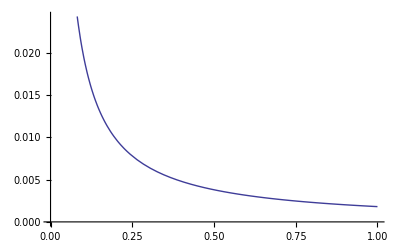

```mathematica
Plot[f[q]/.γ->s Ne/.U->u Ne/.s->-0.0001/.Ne->1000/.u->10^-6,{q,0,1},PlotRange->{0,Automatic}]
```

We are actually more interested in the probability that a mutation that arises once is sampled at frequency q. From equation 1 in Bustamante et al 2001 (Genetics 159:1779), this is

```mathematica
f[q_]:=(1-Exp[-2 γ(1-q)])/(1-Exp[-2γ]) 2/(q(1-q))
```

which is just the previous f[q] with U=1 (ie once the mutation has occured we no longer need to consider the rate at which it appears as we only consider it to appear once).

This looks like:

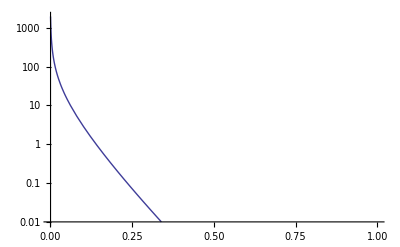

```mathematica
LogPlot[f[q]/.γ->s Ne/.s->-0.0001/.Ne->1000,{q,1/1000,1},PlotRange->{10^-2,All}]
```

We next want to get the CDF from the above PDF

```mathematica
Integrate[f[q],{q,1/n,x},Assumptions->{0<n,1/n<x<1}]
```

1/(-1+ⅇ^(2 γ))2 (ExpIntegralEi[(2 γ)/n]-ⅇ^(2 γ) ExpIntegralEi[-(2 (-1+n) γ)/n]+ⅇ^(2 γ) ExpIntegralEi[2 (-1+x) γ]-ExpIntegralEi[2 x γ])+(1+Coth[γ]) Log[-((-1+n) x)/(-1+x)]

```mathematica
cdf[x_]:=1/(-1+ⅇ^(2 γ))2 (ExpIntegralEi[(2 γ)/n]-ⅇ^(2 γ) ExpIntegralEi[-(2 (-1+n) γ)/n]+ⅇ^(2 γ) ExpIntegralEi[2 (-1+x) γ]-ExpIntegralEi[2 x γ])+(1+Coth[γ]) Log[-((-1+n) x)/(-1+x)]
```

we can then use the inverse transform method to sample from the pdf (choose a random number u uniformly from (0,1) and calculate what x solves cdf[x] = u)

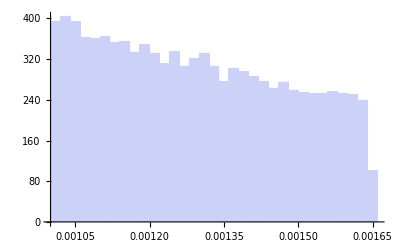

```mathematica
nnums=10^4;
Table[Random[Real],{x,nnums}];
Table[x/.FindRoot[cdf[x]-rv/.rv->%[[i]]/.γ->-0.1/.n->1000,{x,0.5}],{i,1,nnums}];
Histogram[%]
```

and we see this matches the pdf (y-axis numbers do not align since above we have a histogram (ie does not sum to one) from a finite sample (does not sample from range where probability very low))

```mathematica
NIntegrate[f[q]/.γ->-0.1,{q,1/1000,0.0017}]
```

1.06111

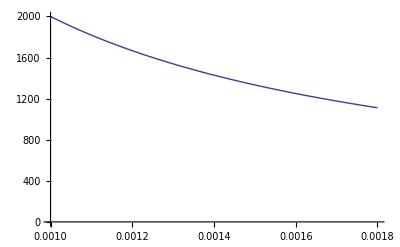

```mathematica
Plot[ f[q]/.γ->-0.1,{q,1/1000,0.0018},PlotRange->{0,Automatic}]
```

try to get expected value...

```mathematica
Integrate[q(1-Exp[-2 γ(1-q)])/(1-Exp[-2γ]) 2/(q(1-q)),{q,0+1/n,1-1/n}]
```

ConditionalExpression[1/(-1+ⅇ^(2 γ))2 ⅇ^(2 γ) (ExpIntegralEi[-(2 γ)/n]-ExpIntegralEi[-(2 (-1+n) γ)/n]+Log[1-n]-Log[-1/n]+Log[1/n]),(Re[(1-n)/(-2+n)]<-1||Re[(-1+n)/(-2+n)]<0||(1-n)/(-2+n)∉Reals||(-1+n)/(-2+n)∉Reals)&&(Re[(-1+n)/(-2+n)]≥1||Re[(-1+n)/(-2+n)]≤0||(-1+n)/(-2+n)∉Reals)&&(Im[n] Im[γ]+Re[n] Re[γ])/(Im[n]^2+Re[n]^2)≥Re[γ]&&Im[n] Im[γ]+Re[n] Re[γ]≤0]

```mathematica
1/(-1+ⅇ^(2 γ))2 ⅇ^(2 γ) (ExpIntegralEi[-(2 γ)/n]-ExpIntegralEi[-(2 (-1+n) γ)/n]+Log[1-n]-Log[-1/n]+Log[1/n])/.γ->-0.1/.n->1000
```

1.89736+0. ⅈ